```mathematica
(*TI5 *)
(*look at fitting with Gasussian process, Pade, power series*)
(*Integrate with Gaussian quadrature and normal quadrature*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4730","T_dudl_meam_4759","T_dudl_meam_4801","T_dudl_meam_4850"};
TdUdL=Table[ReadList[filesEinsteinPot[[i]],{Number, Number}],{i,1,5}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols={4.685,4.730,4.759,4.801,4.850};
ListPlot[Table[Transpose[TdUdL[[i]]][[2]],{i,1,5}],PlotLabel->"ZrC dU/dλ for 6 temperatures: 300 K to 3805 K",AxesLabel->{"dU/dλ index \n(at six T)","dU/dλ value"},ImageSize->800,PlotLegends->SwatchLegend[vols]]
```

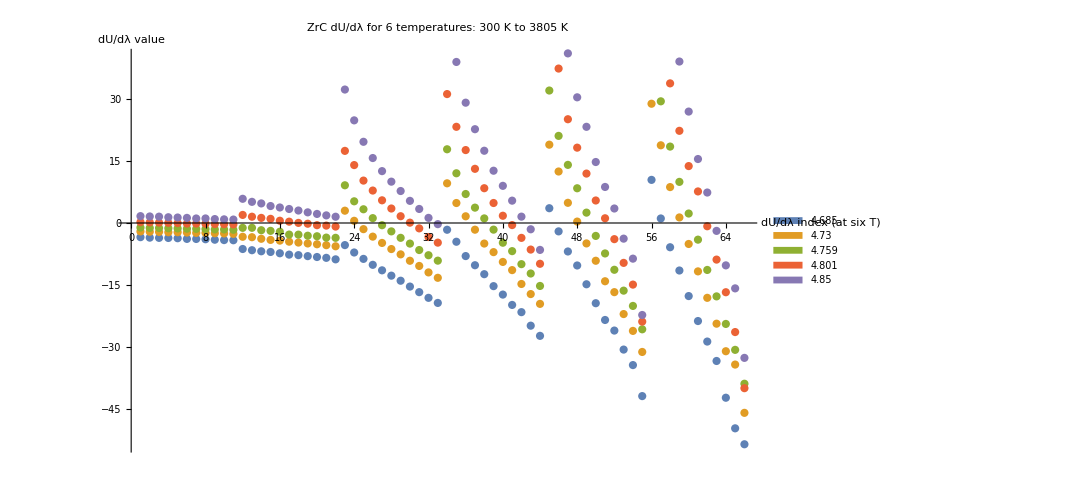

{{0.,79.551},{0.1,58.4269},{0.2,41.0794},{0.3,30.4408},{0.4,23.2966},{0.5,14.77},{0.6,8.72762},{0.7,3.51085},{0.8,-3.79248},{0.9,-8.63635},{1.,-22.2838}}

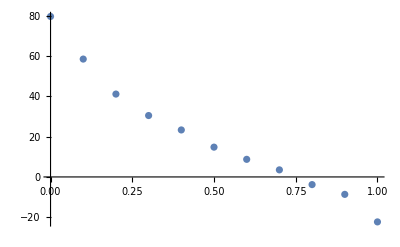

```mathematica
(*Test with 4.685 dudl at 3805*)
testdudl=Transpose[{lambda,Partition[Transpose[TdUdL[[5]]][[2]],11][[5]]}]
ListPlot@testdudl
```

19.6635

20.4628

19.5288

19.5288

19.5159

{19.6993}

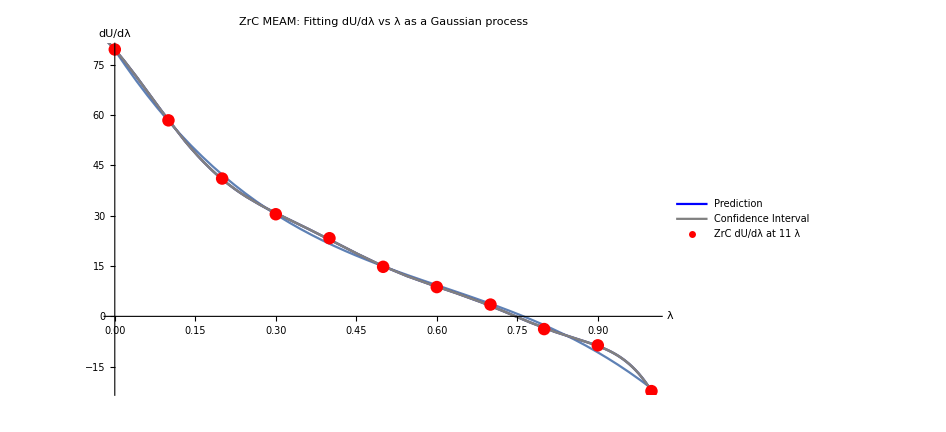

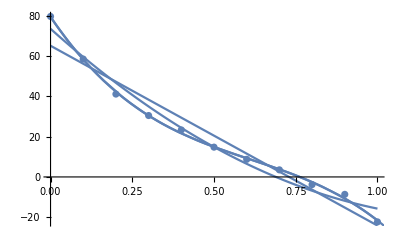

```mathematica
NIntegrate[Evaluate@Interpolation[testdudl,x],{x,0,1}]
NIntegrate[Evaluate@Fit[testdudl,{1,x},x],{x,0,1}]
NIntegrate[Evaluate@Fit[testdudl,{1,x,x^2},x],{x,0,1}]
NIntegrate[Evaluate@Fit[testdudl,{1,x,x^2,x^3},x],{x,0,1}]
NIntegrate[Evaluate@Fit[testdudl,{1,x,x^2,x^3,x^4},x],{x,0,1}]
data=Flatten[{#1->#2}&@@@testdudl];p=Predict[data,Method->"GaussianProcess"];
NIntegrate[{p[x]},{x,-0.0,1.0}]

plotoptions1={AxesLabel->{"λ","dU/dλ"},ImageSize->700,PlotLabel->"ZrC MEAM: Fitting dU/dλ vs λ as a Gaussian process"};
Show[Plot[Evaluate@Fit[testdudl,{1,x,x^2,x^3,x^4},x],{x,0,1}],Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,-0.05,1.05},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"ZrC dU/dλ at 11 λ"}],Evaluate@plotoptions1]

Show[ListPlot@testdudl,Plot[Evaluate@Fit[testdudl,{1,x},x],{x,0,1}],Plot[Evaluate@Fit[testdudl,{1,x,x^2},x],{x,0,1}],Plot[Evaluate@Fit[testdudl,{1,x,x^2,x^3},x],{x,0,11}],Plot[Evaluate@Fit[testdudl,{1,x,x^2,x^3,x^4},x],{x,0,1}]]
```